```mathematica
mVToDegrees[voltage_, tempConst_]:=voltage/tempConst*1000;
```

```mathematica
mVToDegrees[44.27,41]
```

1079.76

```mathematica
A=({{44.27}, {44.49}, {44.66}, {44.45}, {44.31}});
B=mVToDegrees[#,41]&/@A
```

{{1079.76},{1085.12},{1089.27},{1084.15},{1080.73}}

```mathematica
26+#&/@B
```

{{1105.76},{1111.12},{1115.27},{1110.15},{1106.73}}

```mathematica
MatrixForm[{{1105.7560975609756},{1111.1219512195123},{1115.2682926829266},{1110.1463414634147},{1106.7317073170732}}]
```

(1105.76
1111.12
1115.27
1110.15
1106.73)

```mathematica
Indexes=MatrixForm[Table[i,{i,10}]]
```

(1
2
3
4
5
6
7
8
9
10)

```mathematica
TCelsium=({{957}, {1090}, {1182}, {1296}, {1445}, {1578}, {1679}, {1783}, {1886}, {1922}});
WLamp=({{40}, {50}, {60}, {90}, {110}, {150}, {170}, {190}, {230}, {240}});
Current=({{0.8}, {0.894}, {0.962}, {1.157}, {1.263}, {1.368}, {1.546}, {1.615}, {1.735}, {1.753}});
Voltage=({{26.65}, {34.48}, {40.44}, {58.65}, {69.41}, {80.40}, {101.34}, {109.74}, {125.32}, {127.71}});
```

```mathematica
TKelvin=273+#&/@TCelsium
```

{{1230},{1363},{1455},{1569},{1718},{1851},{1952},{2056},{2159},{2195}}

```mathematica
PowerW=Current*Voltage
```

{{21.32},{30.8251},{38.9033},{67.8581},{87.6648},{109.987},{156.672},{177.23},{217.43},{223.876}}

```mathematica
σPower=(0.03*#&/@Current)+(0.001*#&/@Voltage)
```

{{0.05065},{0.0613},{0.0693},{0.09336},{0.1073},{0.12144},{0.14772},{0.15819},{0.17737},{0.1803}}

```mathematica
TtermK=800+1.057*(#&/@TKelvin-790)
```

{{1265.08},{1405.66},{1502.91},{1623.4},{1780.9},{1921.48},{2028.23},{2138.16},{2247.03},{2285.09}}

```mathematica
LnT=Log[#&/@TtermK]
```

{{7.14289},{7.24826},{7.31516},{7.39228},{7.48487},{7.56085},{7.61492},{7.6677},{7.71737},{7.73416}}

```mathematica
LnW=Log[#&/@PowerW]
```

{{3.05965},{3.42833},{3.66108},{4.21742},{4.47352},{4.70036},{5.05415},{5.17745},{5.38188},{5.41109}}

```mathematica
Grp=LnT.({{1, 0}})+LnW.({{0, 1}})
```

{{7.14289,3.05965},{7.24826,3.42833},{7.31516,3.66108},{7.39228,4.21742},{7.48487,4.47352},{7.56085,4.70036},{7.61492,5.05415},{7.6677,5.17745},{7.71737,5.38188},{7.73416,5.41109}}

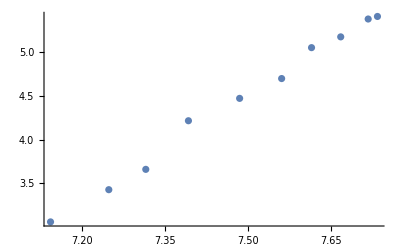

```mathematica
ListPlot[Grp]
```

```mathematica
S=Normal[LinearModelFit[Grp,x,x]]
```

-26.0655+4.0762 x

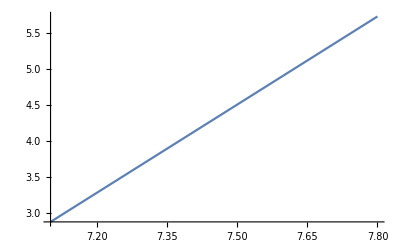

```mathematica
Lin=Plot[S,{x,7.1,7.8}]
```

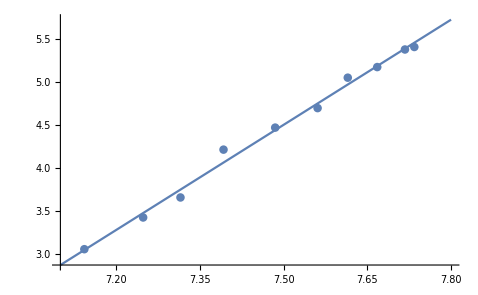

```mathematica
Show[Lin,ListPlot[Grp], PlotTheme->"Detailed"]
```

```mathematica
Tabl=MatrixForm[TKelvin.({{1, 0, 0, 0, 0, 0, 0, 0}})+TtermK.({{0, 1, 0, 0, 0, 0, 0, 0}})+Current.({{0, 0, 1, 0, 0, 0, 0, 0}})+Voltage.({{0, 0, 0, 1, 0, 0, 0, 0}})+PowerW.({{0, 0, 0, 0, 1, 0, 0, 0}})+σPower.({{0, 0, 0, 0, 0, 1, 0, 0}})+LnT.({{0, 0, 0, 0, 0, 0, 1, 0}})+LnW.({{0, 0, 0, 0, 0, 0, 0, 1}})]
```

(1230. | 1265.08 | 0.8 | 26.65 | 21.32 | 0.05065 | 7.14289 | 3.05965
1363. | 1405.66 | 0.894 | 34.48 | 30.8251 | 0.0613 | 7.24826 | 3.42833
1455. | 1502.91 | 0.962 | 40.44 | 38.9033 | 0.0693 | 7.31516 | 3.66108
1569. | 1623.4 | 1.157 | 58.65 | 67.8581 | 0.09336 | 7.39228 | 4.21742
1718. | 1780.9 | 1.263 | 69.41 | 87.6648 | 0.1073 | 7.48487 | 4.47352
1851. | 1921.48 | 1.368 | 80.4 | 109.987 | 0.12144 | 7.56085 | 4.70036
1952. | 2028.23 | 1.546 | 101.34 | 156.672 | 0.14772 | 7.61492 | 5.05415
2056. | 2138.16 | 1.615 | 109.74 | 177.23 | 0.15819 | 7.6677 | 5.17745
2159. | 2247.03 | 1.735 | 125.32 | 217.43 | 0.17737 | 7.71737 | 5.38188
2195. | 2285.09 | 1.753 | 127.71 | 223.876 | 0.1803 | 7.73416 | 5.41109)

```mathematica
TeXForm[Tabl]
```

\left(
\begin{array}{cccccccc}
 1230. & 1265.08 & 0.8 & 26.65 & 21.32 & 0.05065 & 7.14289 & 3.05965 \\
 1363. & 1405.66 & 0.894 & 34.48 & 30.8251 & 0.0613 & 7.24826 & 3.42833 \\
 1455. & 1502.91 & 0.962 & 40.44 & 38.9033 & 0.0693 & 7.31516 & 3.66108 \\
 1569. & 1623.4 & 1.157 & 58.65 & 67.8581 & 0.09336 & 7.39228 & 4.21742 \\
 1718. & 1780.9 & 1.263 & 69.41 & 87.6648 & 0.1073 & 7.48487 & 4.47352 \\
 1851. & 1921.48 & 1.368 & 80.4 & 109.987 & 0.12144 & 7.56085 & 4.70036 \\
 1952. & 2028.23 & 1.546 & 101.34 & 156.672 & 0.14772 & 7.61492 & 5.05415 \\
 2056. & 2138.16 & 1.615 & 109.74 & 177.23 & 0.15819 & 7.6677 & 5.17745 \\
 2159. & 2247.03 & 1.735 & 125.32 & 217.43 & 0.17737 & 7.71737 & 5.38188 \\
 2195. & 2285.09 & 1.753 & 127.71 & 223.876 & 0.1803 & 7.73416 & 5.41109 \\
\end{array}
\right)

```mathematica
LinearModelFit[Grp,x,x]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -26.0655 | 0.923668 | -28.2195 | 2.68654×10^-9
x | 4.0762 | 0.123314 | 33.0556 | 7.65344×10^-10

```mathematica
σF[W_,T_]:=(W*10000)/(getE[T]*0.36*T^4);
```

```mathematica
ClearAll[σ]
hPlank[σ_]:=((2*π^5*1.38^4)/(15*3^2 σ))^(1/3);
```

```mathematica
eT=({{800, 0.067}, {900, 0.081}, {1000, 0.105}, {1100, 0.119}, {1200, 0.133}});
Normal[LinearModelFit[eT,T,T]]
```

-0.069+0.00017 T

```mathematica
getE[T_]:=-0.051076923076922826+0.00015208791208791192T;
```

```mathematica
getE[900]
```

0.0858022

```mathematica
SB=σF[PowerW,TtermK]
```

{{1.63602×10^-6},{1.34795×10^-6},{1.19335×10^-6},{1.38589×10^-6},{1.10151×10^-6},{9.29394×10^-7},{9.99123×10^-7},{8.593×10^-7},{8.15042×10^-7},{7.69367×10^-7}}

```mathematica
planks=hPlank[SB]
```

{{215.803},{230.195},{239.735},{228.075},{246.221},{260.568},{254.359},{267.468},{272.225},{277.508}}

```mathematica
SBs[σ_,W_]=W*((0.03/σ)^2+16*(0.01)^2)^0.5
sPlank[h_,ssig_,sig_]:=h*ssig/(3*sig);
sbs=SBs[SB,PowerW];
```

W (0.0016+0.0009/σ^2)^0.5

```mathematica
MatrixForm[TtermK.({{1, 0, 0, 0, 0}})+SB.({{0, 1, 0, 0, 0}})+sbs.({{0, 0, 1, 0, 0}})+planks.({{0, 0, 0, 1, 0}})+sPlank[planks,sbs,SB].({{0, 0, 0, 0, 1}})]
```

(1265.08 | 1.63602×10^-6 | 390948. | 215.803 | 1.71896×10^13
1405.66 | 1.34795×10^-6 | 686045. | 230.195 | 3.9053×10^13
1502.91 | 1.19335×10^-6 | 978003. | 239.735 | 6.54913×10^13
1623.4 | 1.38589×10^-6 | 1.4689×10^6 | 228.075 | 8.05785×10^13
1780.9 | 1.10151×10^-6 | 2.38758×10^6 | 246.221 | 1.77899×10^14
1921.48 | 9.29394×10^-7 | 3.55029×10^6 | 260.568 | 3.3179×10^14
2028.23 | 9.99123×10^-7 | 4.70427×10^6 | 254.359 | 3.99209×10^14
2138.16 | 8.593×10^-7 | 6.18748×10^6 | 267.468 | 6.41977×10^14
2247.03 | 8.15042×10^-7 | 8.00315×10^6 | 272.225 | 8.9102×10^14
2285.09 | 7.69367×10^-7 | 8.72961×10^6 | 277.508 | 1.04958×10^15)

```mathematica
D[(2π*c^2 h)/λ^5*1/(Exp[(h c)/(λ*k*T)]-1),λ]
```

(2 c^3 ⅇ^((c h)/(k T λ)) h^2 π)/((-1+ⅇ^((c h)/(k T λ)))^2 k T λ^7)-(10 c^2 h π)/((-1+ⅇ^((c h)/(k T λ))) λ^6)

```mathematica
Simplify[%33]
```

(2 c^2 h π (c ⅇ^((c h)/(k T λ)) h-5 (-1+ⅇ^((c h)/(k T λ))) k T λ))/((-1+ⅇ^((c h)/(k T λ)))^2 k T λ^7)